```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doWarn=False;
doPlot=True;
doSpace=True;
doEPlot=True;

showMistakes=False;
fps=0;

(** Adaptivity **)
BoostRatio=1.1; (*'Impatience' Multiplier to increase factor when error is not increasing*)
RefineRatio=0.95;(*'Caution' Multiplier to decrease factor when error is increasing*)
MaxRefines=1000;(*Give up refining if refined too many times in a row*)
ErrorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)

(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.01;

(* Tracker values *)
historyAmt=300;

(*Display*)
GradientPerf="Speed";
dispGradientRange=1.;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_,forceData_,arbitfunc_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SamplingSet=N@Range@DataLength/N@SamplingRate;
(* Else *),
SamplingSet=N@Range@DataLength/N@SamplingRate;
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];
(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions if there is no arbitrary minimizing function, of course *)
doArbitraryFitting=(arbitfunc=!={});
If[doArbitraryFitting,
eFunc=N@arbitfunc,
eFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]]]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
TotalRefines=0;
factor=factorx;
dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;
ConsecRefines=0;
(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};
err=eFunc@@iterParams;
prevErr=err+1.;
dir=gFunc@@iterParams;
debugErr={err};
doPerturb=False;
AError=(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(DataLength-varamt))^0.5;
);
LinePlot[points_, size_,amount_]:=Show[ListPointPlot3D[{If[amount>0&&size>amount,points[[-amount;;-1]],points]},PlotRange->All,ImageSize->Medium],Graphics3D@Line@points];
RefreshSPlot[goal_.]:=Module[{dims=Take[#,2]&/@debugParams},SPlot=Evaluate@ContourPlot[
eFunc@@{x,y,0},
Evaluate@({x,-1.+Min@#,1.+Max@#}&@(First/@dims)),
Evaluate@({y,-1.+Min@#,1.+Max@#}&@(Last/@dims)),
PlotLegends->Automatic,PerformanceGoal->goal,ImageSize->300,PlotRange->All];];
SLinePlot[points_,size_,amount_]:=Show[SPlot,Graphics@Line@(If[amount>0&&size>amount,points[[-amount;;-1]],points])];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[
ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->GradientPerf],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]}]
];
(* Realtime monitor plot *)
displayGradientNorm[xV_,yV_,ϵ_]:=Show[
ContourPlot[Norm[gFunc @@ ReplacePart[iterParams, {xV->x,yV->y}]],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
RegionFunction->Function[{x,y,z},z≤ϵ], PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->GradientPerf],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]}]
];
Visualize[]:=
Dynamic@Grid[{
{"Data vs Function","Parameter Space","Error over iterations"},
{If[doArbitraryFitting,"Arbitrary Optimization",ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium,PlotLegends->None]],
If[doPoint,Which[
varamt==3,LinePlot[debugParams,totalIter,historyAmt],
varamt==2,SLinePlot[debugParams,totalIter,historyAmt],
True,"Incorrect dimensionality"],"Disabled"],
If[doEPlot,ListLogLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]},
{"Parameters, nGrad, dir, Delta","Iterations, factor, corrections"},
{Column[{iterParams,-dir,-factor*dir,-factor*SmoothingFunction[dirs]}],
Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/MaxRefines]}],
{AError,prevErr}}
},Frame->All,ItemSize->30];
RefineFactor[]:=(factor*=RefineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;);
BoostFactor[]:=(factor*=BoostRatio^AccelBoost;prevErr=err;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;);
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];

Iterate[n_,tolerance_,min_]:=Module[{i=0},
While[ConsecRefines<MaxRefines&&(i<n &&(NoErr||AError>tolerance&&Norm@dir>min)),
(* Obtain vector from gradient and assign into running array *)
dirs=Prepend[Drop[dirs,-1],dir=gFunc@@iterParams];
ReportIteration[i];(*Report*)If[fps≠0&&ConsecRefines==0,Pause[fps];];(*Pause*)
If[showMistakes,AddToHistory[];];
(*Mark down boost vs error - please do not change other variables*)
iterParams-=factor*SmoothingFunction[dirs];
If[doPerturb,iterParams+=Normalize[RandomReal[1.,varamt]]/dir.dir];
If[ConsecRefines==0,i++;totalIter++;];
err=eFunc @@ iterParams;
AError=(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(DataLength-varamt))^0.5;
(* Factor Adaptivity - check to see whether error has increased over ErrorRatio to determine whether to boost or refine *)
(*Probably should improve the line search to find the actual minimum instead of blundering around wildly *)
If[err/prevErr>ErrorRatio,
(*If err increased, revert, refine, and retry*)
iterParams=debugParams[[-1]];If[Log10[factor]<-100,factor=0.5];RefineFactor[];,
If[!showMistakes,AddToHistory[]];BoostFactor[];];
]];

HDFD[index_]:=Abs@Fourier[Data*Exp[2I π(index-2)N@(Range@DataLength-1)/DataLength],FourierParameters->{0,2/DataLength}];
FindMax[list_]:=Position[list,Max@list][[1,1]];
FindIndexFreq[index_]:=N@((#-2+2(FindMax@HDFD@#-1)/DataLength)*2π*SamplingRate/DataLength)&/@index;
RecoverIndices[]:=First/@(Take[#,Round[(Length@#)/2.]]&@FindPeaks@Abs@Fourier@Data);
RecoverFreqList[]:=(Select[RecoverIndices[],#>0&]//FindIndexFreq);
RecoverDataFreq[i_]:=If[i≤Length@#,#[[i]],#[[Length@#]]]&@RecoverFreqList[];
```

```mathematica
RecordedComparisonData={};
```

```mathematica
(* SET DATA *)
varamt=2;
DataLength=100;
SamplingRate=100;
Fitfunction=Exp[#1*#2]+#3&;
InitFunctionData[5.,{},0.2,NormalDistribution[1,0.25],{},{}];
TrueParams
```

{-4.69059,-4.60356}

```mathematica
(* BEGIN ITERATION *)
InitIterationSettings[];
Smoothness=5;
showMistakes=False;
historyAmt=0;
Balance=1.03;
Impatience=1.08;
BoostRatio=(Balance*Impatience)^0.5;
RefineRatio=(Balance/Impatience)^0.5;

SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;
InitIterationData[0.01,{-2.,1.}];
doPerturb=False;
RefreshSPlot["Speed"];
Column[{
Visualize[],
ToSpacedString@{"Balance: ",Balance=RefineRatio*BoostRatio},
ToSpacedString@{"Impatience: ",Impatience=BoostRatio/RefineRatio},
ToSpacedString@{"Frequency indices: ", RecoverIndices[]},
ToSpacedString@{"Data frequencies: ", RecoverFreqList[]},
ToSpacedString@{"TrueParams",TrueParams}
}]
```

Balance:  1.03
Impatience:  1.08
Frequency indices:  {1, 12, 15, 17, 22, 24, 26, 32, 35, 40, 44, 49}
Data frequencies:  {0., 65.9734, 84.6973, 97.3894, 128.805, 141.372, 160.096, 191.763, 216.77, 248.186, 267.161, 304.609}
TrueParams {-4.69059, -4.60356}

```mathematica
(*** Iteration loop ***)

(* Iterator and maximum values *)
SmallErr=0.001;
NoErr=False;
fps=1./60.;
(* Iteration *)
Iterate[1000,SmallErr,10.^-9]//AbsoluteTiming
RefreshSPlot["Quality"];
```

{46.5261,Null}

```mathematica
If[Length@lines==0,lines={}];
lines=Append[lines,{debugParams,{Balance,Impatience}}];
Show[SPlot,Graphics[{Hue@(Last@#-0.5),Line@First@#}&/@lines]]
```

-Graphics-

```mathematica
(** Data Recording **)
RecordedComparisonData=Catenate[{RecordedComparisonData,
{{{"Smoothness",Smoothness},
debugErr,debugParams,TotalRefines,
{"Balance",Balance},{"Impatience",Impatience},{"Iterations",totalIter}}}}];
```

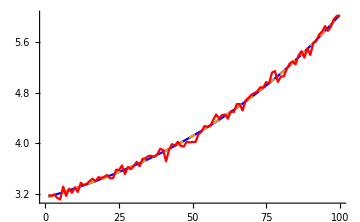

-Graphics3D-

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
Data},
Joined->True,ImageSize->Medium,PlotStyle->{Blue,Dashed,Red}]
LinePlot[debugParams,Length@debugParams,Length@debugParams]
```

$Aborted

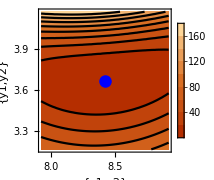

```mathematica
dispGradientRange=0.5;
dispGradientThresh=1.5;
GradientPerf="Performance";
Which[
varamt==3,
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]};
{displayGradientNorm[1,2,dispGradientThresh],displayGradientNorm[2,3,dispGradientThresh],displayGradientNorm[3,1,dispGradientThresh]};,
varamt==2,
displayGradient[1,2];
displayGradientNorm[1,2,dispGradientThresh]
]
displayGradient[1,2]
```

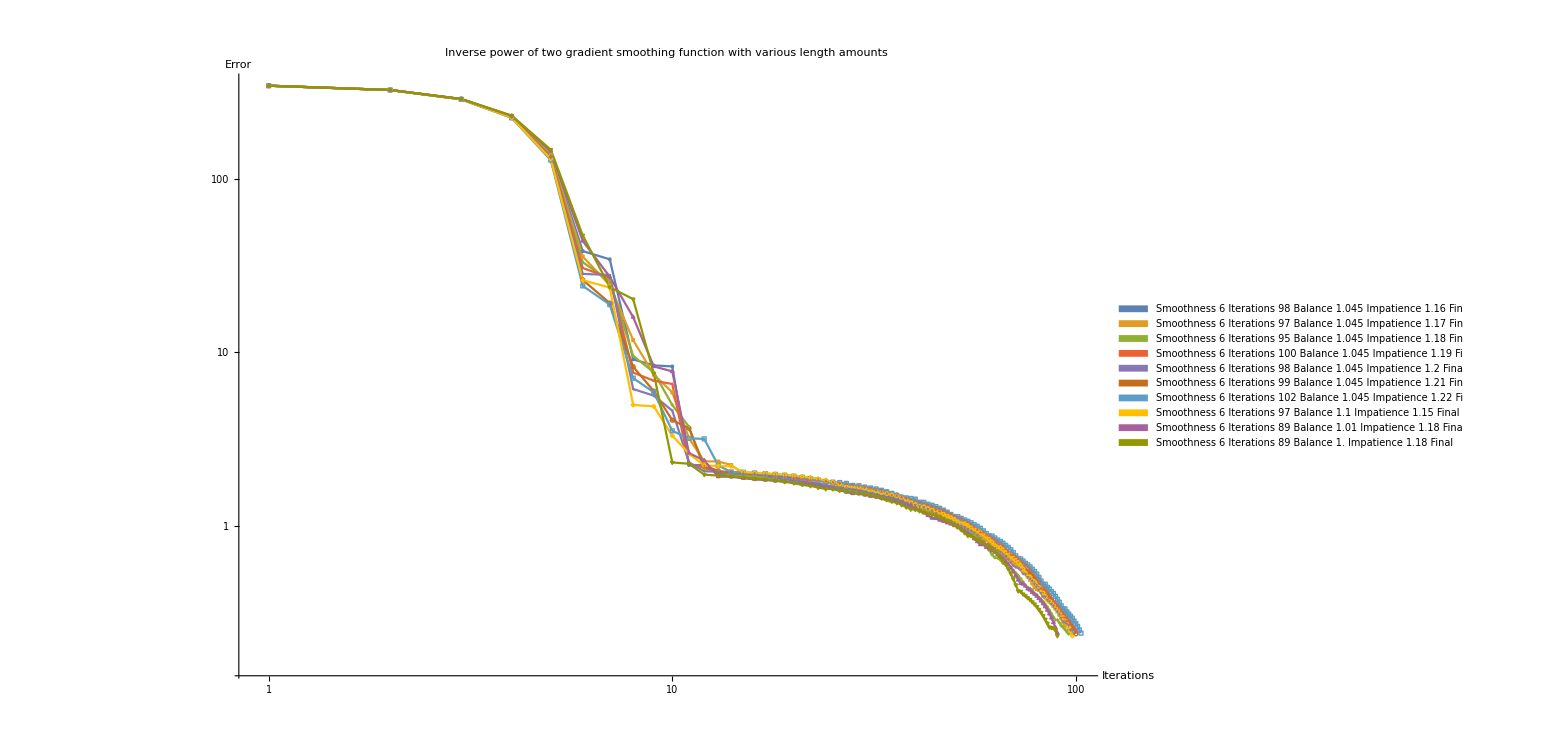

```mathematica
ListLogLogPlot[
Table[RecordedComparisonData[[sm,2]],{sm,1,Length@RecordedComparisonData}],PlotLegends->SwatchLegend[
Table[
Column[
Join[
Flatten@ToSpacedString/@RecordedComparisonData[[sm,{1,7,5,6}]],
{ToSpacedString@{"Final error:",Last@RecordedComparisonData[[sm,2]]},
ToSpacedString@{"Corrections:",RecordedComparisonData[[sm,4]]}}
]
],{sm,1,Length@RecordedComparisonData}],
LegendFunction->"Panel",
LegendLayout->"Row"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},
PlotRange->All,
ImageSize->1200,
Joined->True,
PlotMarkers->{Automatic,4}]
```

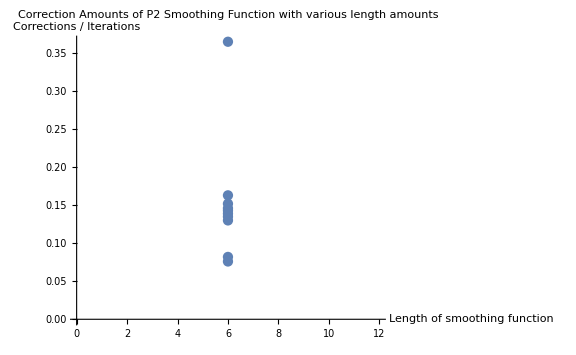

```mathematica
ListPlot[
Table[{RecordedComparisonData[[sm,1,2]],RecordedComparisonData[[sm,4]]/1000.},{sm,1,Length@RecordedComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},
PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",
ImageSize->Large
]
```